## Schrodinger Equation — Hydrogen Wave Functions

## Analyzed in class, May 2, 2025

This is our twenty-fifth and last notebook. To warm up to Schrodinger’s equation in multiple dimensions, we looked at a particle that is free but confined to a two-dimensional disk. The idea was to show you a problem that has some of the flavor of the full three-dimensional problem. Now we will analyze a deservedly-famous three-dimensional problem in quantum mechanics: the Hydrogen atom, and use Mathematica to visualize the three-dimensional wave functions.

### Time-Independent Schrodinger Equation in Three Dimensions

To go to three dimensions we now have second derivatives with respect to x, y, and z:

```mathematica
-ℏ^2/(2μ)(Derivative[2,0,0][ψ][x,y,z]+Derivative[0,2,0][ψ][x,y,z]+Derivative[0,0,2][ψ][x,y,z])+potential[x,y,z]ψ[x,y,z]==energy ψ[x,y,z] // TraditionalForm
```

potential(x,y,z) ψ(x,y,z)-(ℏ^2 (ψ^(0,0,2)(x,y,z)+ψ^(0,2,0)(x,y,z)+ψ^(2,0,0)(x,y,z)))/(2 μ)==energy ψ(x,y,z)

### Spherical Polar Coordinates

Just as in Harper and Tahm’s External Rifle Ballistics notebook, it makes a load of progress toward a solution to switch to spherical polar coordinates. The Wikipedia has a nice graphic:
-Graphics-

The only thing to note about the Wikipedia’s graphic is that we usually have the x-coordinate pointing right, and the y-coordinate going into the paper, so you have to imagine rotating the coordinates by 90.ba (counter-clockwise looking down on the x-y plane), relative to what the Wikipedia has shown.

Now that we know what polar coordinates are, there is another, even nastier calculation that determines how the sum of three second derivatives becomes a sum of derivatives with respect to r, θ, and ϕ:

(∂^2 ψ)/(∂x^2)+(∂^2 ψ)/(∂y^2)+(∂^2 ψ)/(∂z^2)=(∂^2 ψ)/(∂r^2)+2/r(∂ψ)/(∂r)+1/(r^2 sin^2 θ)(sinθ(∂^2 ψ)/(∂θ^2)+cosθ(∂ψ)/(∂θ))+1/(r^2 sin^2 θ)(∂^2 ψ)/(∂ϕ^2))

Of course, I am not going to mess with that. You just have to trust that this combination of derivatives is what comes out of a lot of multi-variable calculus.

### Electron Orbiting a Hydrogen Nucleus

The above theory lets us rewrite, in polar coordinates, the time-independent Schrodinger equation for an electron orbiting a Hydrogen nucleus:

```mathematica
hydrogenAtomProblem=Module[{ℏ=1,μ=1},-ℏ^2/(2μ)(Derivative[2,0,0][ψ][r,θ,ϕ]+2/r Derivative[1,0,0][ψ][r,θ,ϕ]+1/(r^2 Sin[θ]^2)(Sin[θ]Derivative[0,2,0][ψ][r,θ,ϕ]+Cos[θ]Derivative[0,1,0][ψ][r,θ,ϕ])+1/(r^2 Sin[θ]^2)Derivative[0,0,2][ψ][r,θ,ϕ])+potential[r]ψ[r,θ,ϕ]==energy ψ[r,θ,ϕ]] ;
```

Typesetting this equation for Mathematica makes it look even more complicated than it already is, so here is a screenshot of the combination of second derivatives from Howard Haber’s UC Santa Cruz Physics 116C class.

He uses some special notation that I won’t get into (this is just an advertisement for taking an advanced calculus course) to make the second-derivatives especially elegant:

-Graphics-

### The Great Simplification Again — Separation of Variables

Once again our next step is the “separation of variables” trick. We guess that ψ(r,θ,ϕ)=R(r)Θ(θ)Φ(ϕ).

To save myself a bunch of time-consuming typesetting, I am again going to screenshot Howard Haber’s notes:

-Graphics-

### Adding the Boundary Conditions

Some of the boundary conditions have already been mentioned in the screenshotted notes above. In particular, we have to have Φ(2π)=Φ(0). Another boundary condition is that the wave function has to vanish as r->∞. Another boundary condition is that at r=0 where the nucleus is, the wave function can blow up, but only in a very controlled way. The reason it can blow up at all is that the potential is the Coulomb potential which is

V(r)=-e^2/(4 πϵ_0)1/r

and this potential blows up at r=0. I mention these boundary conditions, because without them you would have no idea where statements like “m must be an integer” come from. You have now worked with boundary conditions enough to know that they commonly result in a discrete set of solutions.

### Quantum Numbers

You will see that there are three integers in the exact solutions of the Hydrogen atom. They correspond to the total energy, the total angular momentum, and the component of the angular momentum around the axis that we have chosen as the polar axis in our polar coordinates.

These integers are called “quantum numbers.” The quantum numbers are important because you have to specify them in order to specify which solution of the Schrodinger equation for the Hydrogen atom you are talking about, and equally importantly, because they correspond to important physical quantities. They are usually denoted as n, l, and m, and their direct correspondence is to the energy, the angular momentum, and the component of the angular momentum in the z-direction of the electron orbiting the Hydrogen nucleus. As we get into the exact solutions, this will become clearer.

### The Exact Solutions — Spherical Harmonics

Without further ado, let’s start writing down the exact solutions. Thanks to the separation of variables trick, they can be written as R(r)Θ(θ)Φ(ϕ), but the Θ(θ)Φ(ϕ) portion is usually grouped together to make functions of θ and ϕ known as the “spherical harmonics.” Traditionally they are written as Y_l^m(θ,ϕ) and happily, Mathematica knows these functions. For example, here is the function with l=3 and m=1:

```mathematica
SphericalHarmonicY[3,1,θ,ϕ]
```

-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ]

The ϕ-dependence is always pleasantly simple, it is just e^imϕ which in this case, with m=1, is just e^iϕ. When you do the complex absolute value of a spherical harmonic, the ϕ-dependence goes away.

Let’s plot a few of these from the north pole (θ=0) to the south pole (θ=π):

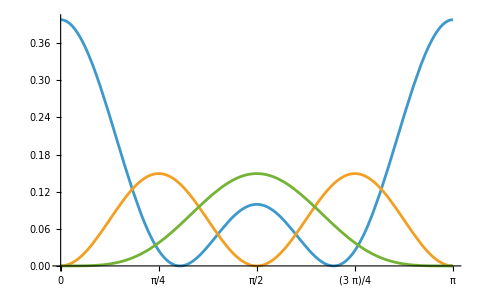

```mathematica
ylmSquared[l_,m_,θ_]:=Abs[SphericalHarmonicY[l,m,θ,0]]^2
Plot[{ylmSquared[2,0,θ],ylmSquared[2,1,θ],ylmSquared[2,2,θ]},{θ,0,Pi},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

Further down in this notebook, we will be doing three-dimensional visualizations, so you don’t have to glean too much from the preceding plots.

However, I could say something about why it is actually intuitive that they have different z-component of angular momentum, but all have the same total angular momentum. Essentially, the ones that bulge the most near the equator (θ=π/2) have most angular momentum in the z-direction, and the ones that bulge near the poles (θ=0 and θ=π) have the least.

### The Exact Solutions — Radial Wave Functions

```mathematica
R[n_,l_,r_]:= 2/n^2 √(Factorial[n-1-l]/Factorial[n+l]^3) ((2 r)/n)^l Exp[-r/n] Factorial[n+l] LaguerreL[n-l-1,2 l+1,2r/n];
```

We’ll be squaring these too, so it might be handy to define:

```mathematica
rnlSquared[n_,l_,r_]:=Abs[R[n,l,r]]^2
```

Let’s look at a few with n=3, and l=0, 1, and 2:

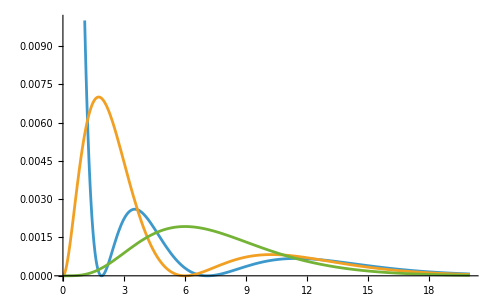

```mathematica
Plot[{rnlSquared[3,0,r],rnlSquared[3,1,r],rnlSquared[3,2,r]},{r,0,20},Ticks->{Range[0,10,1],0,1},PlotRange->{{0,20},{0,0.01}}]
```

When someone starts jabbering away about orbital shells, it is these functions that they are referring to.

### Normalization

The super-messy formulas above were messy in part because these solutions are already normalized, so thankfully, there is no further messiness due to normalization.

I should comment on why it does not appear that each of the spherical harmonics has the same area. It is because there is less area for a given change in latitude near the poles of a sphere than there is at any layer further out. So to see that the spherical harmonics are equally normalized, you have to multiply by an area factor, which is 4 π sin^2θ, and then compare them.

And, I should similarly comment on why it does not appear that all the radial wave functions have the same area. It is because there is less volume for a given change in radius near the center of a sphere than there is at any layer further out. So to see that the radial functions are equally normalized, you have to multiply by another factor, which is r^2, and then compare them.

### Allowed Quantum Numbers and Total Energy

Not all combinations of quantum numbers n,l, and m are allowed. The only ones that correspond to solutions are in these these ranges:

n=1,2,3,4, etc.
l=0,1,2,...,n-1
m=-l,-l+1, ..., -1, 0,1, ..., l-1,l 

The total energy is entirely determined by the value of n and if you choose all the units conveniently the total energy is just -1/n^2. All you need to know to know the energy is n, so it is known as the “principle quantum number.”

You might be wondering what a minus sign is doing in the total energy. It is there because the Coulomb potential is attractive and it gets more and more negative as the electron gets closer to the nucleus. So there is positive kinetic energy and negative potential energy, and the latter outweighs the former for a bound electron.

If you had an electron with total positive energy (kinetic exceeds potential), it would fly away from the Hydrogen atom (leaving the proton sitting alone, as a positive ion).

There is some lovely and nowadays standard counting of how electrons are added, one-by-one into an atom to build up all the atoms in the periodic table. Beware that there is a large naive step in this argument. It uses the Hydrogen atom wave functions which are only valid for when one electron is present. Additional electrons repel each other. The naive counting of quantum states for a given energy level is altered by the mutual repulsion, and nobody knows how to solve any problem exactly that is more complex is Hydrogen. So the explanation of the periodic table is only qualitative, even though there is every reason to be leave that it is substantially correct.

I’m not going to repeat the standard counting argument. I Googled and flipped through a load of crummy references containing the counting argument until I found this quality one from University of Central Florida:

https://pressbooks.online.ucf.edu/osuniversityphysics3/chapter/the-exclusion-principle-and-the-periodic-table/

Instead, we are going to spend the remainder of our last class visualizing the wave functions.

### Visualization — s, p, d, and f Orbitals for the n=4 Principle Quantum Number

The s, p, d, and f orbitals are old names for the l=0, l=1, l=2, and l=3 spherical harmonics. The history is that when experimentalists were discovering the spectral lines of Hydrogen, they named them “sharp,” “principle,” “diffuse,” and “fine.”

The l=0 orbitals aren’t very interesting to visualize because they are spherically symmetric. However, because I have chosen n=4 (which is a little uncommon), there is nevertheless some interesting structure even in this density plot with l=0 .

```mathematica
DensityPlot3D[rnlSquared[4,0,ToSphericalCoordinates[{x,y,z}][[1]]]ylmSquared[0,0,ToSphericalCoordinates[{x,y,z}][[2]]],{x,-30,30},{y,-30,30},{z,-30,30}]
```

-Graphics3D-

If n=4, then l=0, l=1, l=2, and l=3 are allowed, and so n=4, l=1 is the first interesting orbital to visualize. They can have m=-1,0,or +1.

Let’s see if we can visualize the n=4,l=1,m=0 probability distribution:

```mathematica
DensityPlot3D[rnlSquared[4,1,ToSphericalCoordinates[{x,y,z}][[1]]]ylmSquared[1,0,ToSphericalCoordinates[{x,y,z}][[2]]],{x,-30,30},{y,-30,30},{z,-30,30}]
```

-Graphics3D-

To do d orbitals, we can try the n=4,l=2,m=0 probability distribution:

```mathematica
DensityPlot3D[rnlSquared[4,2,ToSphericalCoordinates[{x,y,z}][[1]]]ylmSquared[2,0,ToSphericalCoordinates[{x,y,z}][[2]]],{x,-30,30},{y,-30,30},{z,-30,30}]
```

-Graphics3D-

I want to stress that usually you see these plotted with fewer lobes. The additional lobes shown are because I have chosen the n=4 radial wave functions. You should change n and re-render the wave functions. Of course, when you change n you must follow the allowed quantum number rules for l, which can only go from 0 to n-1.

To do f orbitals, we can try the n=4,l=3,m=0 probability distribution:

```mathematica
DensityPlot3D[rnlSquared[4,3,ToSphericalCoordinates[{x,y,z}][[1]]]ylmSquared[3,0,ToSphericalCoordinates[{x,y,z}][[2]]],{x,-30,30},{y,-30,30},{z,-30,30}]
```

-Graphics3D-

These are famous shapes (although to level the energy playing field I have always chosen n=4 which again I should mention is a little uncommon). Physical chemists spend a lot of time trying to figure out what molecules are likely to form based on how these shapes might interlock with neighboring shapes.

### Time-Dependence

To get time-dependence, we are going to have to make mixtures (superpositions) of quantum states with different energies. Also, this is going to necessitate dealing with the full complex values. Let’s try a mixture of n=2, l=1, and m=+1, n=1, l=0, and m=0, and n=2, l=1, and m=-1 and see what we get.

```mathematica
mixture[t_,r_,θ_,ϕ_]:=1/2 Exp[Sqrt[-1] 1/4 t]R[2,1,r]SphericalHarmonicY[2,1,θ,ϕ]+1/Sqrt[2] Exp[Sqrt[-1]t]R[1,0,r]SphericalHarmonicY[1,0,θ,ϕ]+
1/2 Exp[Sqrt[-1] 1/4 t]R[2,1,r]SphericalHarmonicY[2,-1,θ,ϕ];
mixtureSquared[t_,r_,θ_,ϕ_]:=Abs[mixture[t,r,θ,ϕ]]^2
```

Three-dimensional plots are going to be expensive to animate, so let’s confine ourselves to the θ=π/2 plane and do two-dimensional plots. To further respect computational power, I am going to pre-render these for 40 time steps:

```mathematica
prerenders=Array[DensityPlot[Log[mixtureSquared[(#-1) (8 Pi)/(3 40),ToPolarCoordinates[{x,y}][[1]],Pi/2,ToPolarCoordinates[{x,y}][[2]]]],{x,-5,5},{y,-5,5},MaxRecursion->6,PerformanceGoal->"Quality",ClippingStyle->Automatic,ColorFunction->"Rainbow"]&,40];
```

Once the pre-rendering finishes, we’ll try animation:

```mathematica
Animate[prerenders[[i]],{i,1,40,1},AnimationRunning->False]
```

I should continue working on the quality of this animation if I really want it to show the up and down (y-direction) motion better. The flashing is an artifact caused by changing scale. (I have let Mathematica automatically choose the scale, and it is choosing different scales for different frames of the animation.)

In addition to seeing wave functions going up and down in the y-direction, we should be able to see them going around and around:

```mathematica
anotherMixture[t_,r_,θ_,ϕ_]:=1/Sqrt[2] Exp[Sqrt[-1] 1/4 t]R[2,1,r]SphericalHarmonicY[2,1,θ,ϕ]+1/Sqrt[2] Exp[Sqrt[-1]t]R[1,0,r]SphericalHarmonicY[1,0,θ,ϕ];
anotherMixtureSquared[t_,r_,θ_,ϕ_]:=Abs[anotherMixture[t,r,θ,ϕ]]^2

morePrerenders=Array[DensityPlot[Log[anotherMixtureSquared[(#-1) (8 Pi)/(3 40),ToPolarCoordinates[{x,y}][[1]],Pi/2,ToPolarCoordinates[{x,y}][[2]]]],{x,-5,5},{y,-5,5},MaxRecursion->6,PerformanceGoal->"Quality",ClippingStyle->Automatic,ColorFunction->"Rainbow"]&,40];
```

Once the new pre-rendering finishes, we’ll try that animation too:

```mathematica
Animate[morePrerenders[[i]],{i,1,40,1},AnimationRunning->False]
```

Again there are artifacts that could be improved upon (in this case, I can see some clipping of the scale at the most blue part of the plot), but I am nonetheless pleased to easily get an electron probability distribution to travel in a circle around the nucleus, and I hope you are too.

### Conclusion — What was the Point? — Of this Notebook? — Of this Course?

Well, we have reached the end. If you think stuff like this is insanely cool, you might want to spend a few years getting a degree in physics.

If on the other hand, it was nice, but you have had enough and would rather do something else, then the point of all this was to quickly expose you to some mathematics and problem solutions that you are very unlikely to see unless you become a physicist or a physical chemist, but which are nonetheless incessantly alluded to, like the myths in the Odyssey.

Oscillations and waves are everywhere around us, and you have now seen behind the curtain — with Mathematica’s help in doing large amounts of algebra and computation — into some things that are otherwise not easily revealed.

You also now have a tool — Mathematica — to do quick, high-quality algebra, computation, and visualization for any other problems you might run into. Numerical methods go hand in hand with exact methods to both build insight and test any kind of model, and these methods uniquely come together with a symbolic manipulation system. Even if you never do any other physics, you might build economic models, biological models, or epidemiological models in Mathematica, and let it help you explore and visualize their consequences.

Finally, this is my first time teaching a course where the computer language was Mathematica. Part of the point for me was to grow my fluency in Mathematica as you grow yours. Thank you for letting me do that with you as the test subjects.